```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: PacletObject[…].

It can now be loaded using the command <<IGraphM`

```mathematica
<<IGraphM`;
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]
(*https://mathematica.stackexchange.com/questions/18625/avoiding-grid-lines-inside-filled-area-in-regionplot-exported-as-pdf*)
```

```mathematica
Needs["CUDALink`"];
CUDALink`InstallCUDA[];
CUDALink`CUDAQ[]
```

```mathematica
db = DatabaseReference[FindFile[NotebookDirectory[]<>"/../data/genova.db"]]
```

DatabaseReference[…]

```mathematica
(* We select the absolute, treat F and T roads as the same. This simplifies graph and reduces computation time. Since data is bad anyways, I don't think this will affect the results by much.*)
queryGraphLinks = ExternalEvaluate[db, "
	WITH e(edge_id, node_from_id, node_to_id) AS (
		SELECT geo_edges.edge_id, geo_edges.node_from_id, geo_edges.node_to_id
		FROM geo_edges
		
	), g(edge_id, node_from_id, node_to_id) AS (
		SELECT geo_edges.edge_id, geo_edges.node_from_id, geo_edges.node_to_id
		FROM geo_edges
		
	)
	SELECT ABS(g.edge_id) as \"from\", ABS(e.edge_id) AS \"to\"
	FROM e
	INNER JOIN g
	WHERE e.node_to_id = g.node_from_id AND ABS(g.edge_id) <> ABS(e.edge_id)
	UNION
	SELECT ABS(e.edge_id) AS \"from\", ABS(g.edge_id) as \"to\"
	FROM e
	INNER JOIN geo_edges g
	WHERE e.node_from_id = g.node_to_id AND ABS(g.edge_id) <> ABS(e.edge_id)
;"];

(* We select max because we are interested on the study of the congested direction of the road*)
queryTrafficData = ExternalEvaluate[db, "
	SELECT
		g.edge_id AS edge_id,
		MAX(t.count_mean) AS count
	FROM geo_edges g
	INNER JOIN traffic_data t
	ON g.edge_id = ABS(t.edge_id)
	WHERE t.hour_slot = 170
	GROUP BY g.edge_id
;"];
```

```mathematica
graphLinks = Thread[#["from"]<-> #["to"] /. #]&/@Normal[queryGraphLinks];
g=Graph[graphLinks,VertexLabels->None];
validNodes = queryTrafficData[[;;, 1]];
invalidNodes = Select[VertexList[g], !MemberQ[validNodes, #]&];
g = VertexDelete[g, invalidNodes];
disconnectedNodes = Flatten[ConnectedComponents[g][[2;;]]]; (* Remove disconnected train network *)
g = VertexDelete[g, disconnectedNodes];
```

```mathematica
Rasterize[GraphPlot[g], RasterSize->1000]
```

-Graphics-

```mathematica
Count[VertexDegree[g], 2] (* Are there relatively few nodes with only two degrees? Can we go on without simplifying the graph? *)
```

530

## Getting transition rates

```mathematica
ToAssociations = ResourceFunction["ToAssociations"];
neighborsOf = ToAssociations[# ->VertexList@VertexDelete[NeighborhoodGraph[g, #], #] &/@ VertexList[g]];
carCount =ToAssociations[ #["edge_id"]->#["count"]&/@ Normal[queryTrafficData]];
```

```mathematica
neighborsOf[55262035]
carCount[55262035]
```

{55262034,55262068}

0.193548

### Random walk

For a left stochastic matrix, each column sums to 1.  Values are the probability of moving from node=column to node=row.

Algorithm:
1) Move each agent
2) Check if any node fails
3) immediately, redistribute agents, propagate avalanche
4) End simulaiton

```mathematica
On[Assert]
ClearAll["Pop"];
SetAttributes[Pop,HoldFirst];
Pop[list_]:=With[{item=list[[1]]},list=Delete[list,1];item];

ClearAll["Simulate"];
Simulate[markovMatrix_, nodeCarThresholds_, agentProbabilities_, maxSteps_] := Module[{thresholds, probabilities, rateMatrix, MoveAgents, AreThereFailures , ComputeAvalancheSize, i, nNodes, nAgents, carCounts, singleAgentStates, failedNodes},
thresholds = GPUArray[nodeCarThresholds];
rateMatrix = GPUArray[markovMatrix];
probabilities = GPUArray[agentProbabilities];
nNodes = Length[markovMatrix];

If[nNodes != Length[nodeCarThresholds], Return[$Failed]];

nAgents = Length[agentProbabilities];
singleAgentStates = GPUArray@Eigenvectors[IdentityMatrix[nNodes]]//Reverse;
	
MoveAgents[] := Module[{},
(*rateMatrix.# o #.rateMatrix? Questo è abbastanza importante.... Per ora sembrano uscire gli stessi risultati...*)
probabilities = GPUArray[RandomChoice[rateMatrix.#->singleAgentStates ] &/@ probabilities];
];

AreThereFailures[] := Module[{},
carCounts = Total/@Transpose@probabilities;
failedNodes = Append[(Transpose@Position[# < 0 &/@ (thresholds -carCounts ), True]), {}][[1]];

If[Length[failedNodes]>0, Return[True]];

False
];

ComputeAvalancheSize[node_] := Module[{avalancheSize, carCount, currentCarCounts, adjacentNodes, nodesToCheck, lockedNodes, currentNode, newNode, transitionProbabilities},
nodesToCheck = {node};
lockedNodes = {};
currentCarCounts = carCounts;


While[Length@nodesToCheck >0,
currentNode = Pop[nodesToCheck];
Assert[currentCarCounts[[currentNode]] >0, "carCount"];

If[thresholds[[currentNode]] -currentCarCounts[[currentNode]] >=0, Continue[]];

AppendTo[lockedNodes, currentNode];

If[Length@lockedNodes == nNodes, Break[]];

transitionProbabilities = Normal@rateMatrix[[currentNode]];
(transitionProbabilities[[#]] = 0 )&/@ lockedNodes;
transitionProbabilities /= Total[transitionProbabilities];

For[carCount = currentCarCounts[[currentNode]], carCount >0, carCount--,
Assert[nNodes == Length@transitionProbabilities, "nNodes"];

newNode = RandomChoice[transitionProbabilities->Table[x, {x, 1, nNodes}]];

Assert[newNode != currentNode, "currentNode"];
Assert[!MemberQ[lockedNodes, newNode], "lockedNodes"];
If[!MemberQ[nodesToCheck, newNode], AppendTo[nodesToCheck, newNode]];

currentCarCounts[[newNode]]++;
currentCarCounts[[currentNode]]--;
];
];

Assert[Total[currentCarCounts] == Total[carCounts]];

Return[{node,Length@lockedNodes}];
];

For[i=1, i<=maxSteps,  i++, 
MoveAgents[];

If[!AreThereFailures[], Continue[]];
Break[];
];

If[Length@failedNodes == 0, Return[{}]];

Map[ComputeAvalancheSize, failedNodes]
];
```

Starting simulation

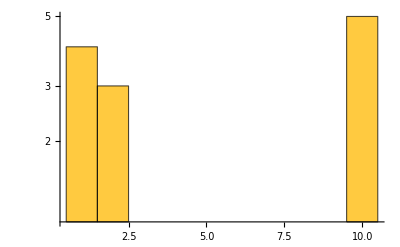

```mathematica
n = 10;
t = 100;
agentCount=12;
sampleCount = 10;

singleAgentStates = Eigenvectors[IdentityMatrix[n]]//Reverse;
GenerateAgents = (nAgents) ↦Table[RandomChoice[singleAgentStates], nAgents];

MarkovMatrix[n_,min_:0]:=If[min n<1,Transpose@RandomPoint[Simplex[IdentityMatrix[n](1-min n)],n]+min,$Failed];
markovMatrix = MarkovMatrix[n];
(*{markovMatrix // MatrixPlot, g = WeightedAdjacencyGraph[markovMatrix]}*)
markovThresholds = Table[RandomInteger[{2, Floor@Sqrt[n]}], n];

(*TODO questa statinary distributoin  non funziona*)
statDist = Re /@ N[Eigenvectors[markovMatrix // Transpose][[1]]];
statDist /= Total[statDist];

Print["Starting simulation"];

(* ;;, ;;, 2 Selects avalanche size, ;;, ;;, 1 selects start node*)
avalancheSizes = ParallelTable[Simulate[markovMatrix,markovThresholds, GenerateAgents[agentCount], t], sampleCount, Method->"FinestGrained"][[;;, ;;, 2]] // Flatten ;
Histogram[avalancheSizes,{1}, ScalingFunctions->"Log", ScalingFunctions->{"Log", "Log"}, PlotRange->Full  ]
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

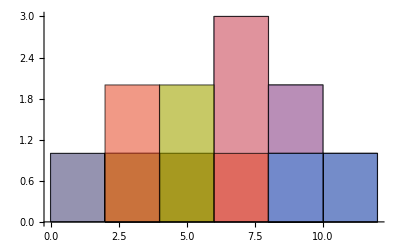

```mathematica
(*Pocci*)
proc = DiscreteMarkovProcess[statDist // Flatten, markovMatrix];
data = RandomFunction[proc, {0, 2}, agentCount];
Histogram[data]
```

```mathematica
data
```

TemporalData[…]

```mathematica
Mean[EstimatedProcess[data, HiddenMarkovProcess[n, n*n]][[2]] - markovMatrix // Flatten]
Variance[EstimatedProcess[data, HiddenMarkovProcess[n, n*n]][[2]] - markovMatrix // Flatten]
Mean[markovMatrix // Flatten]
Variance[markovMatrix // Flatten]
```

-1.11022×10^-18

0.0821193

0.1

0.00745779

## Fundamental Diagram

```mathematica
GetSpeedAndDensityOfSingleRoad = (edgeId) ↦ Module[{queryNodeCapacity, fluxValues, densityValues},
queryNodeCapacity = ExternalEvaluate[db, "
		SELECT
			t.hour_slot as time, AVG(t.count_mean / g.edge_length) AS density, AVG(t.speed_mean)*AVG(t.count_mean / g.edge_length) AS flux
		FROM traffic_data t
		INNER JOIN geo_edges g
		ON g.edge_id = t.edge_id AND ABS(t.edge_id) = "<>ToString[edgeId]<>"
		GROUP BY t.hour_slot
	;"];
fluxValues = Normal@Transpose[queryNodeCapacity]["flux"];
densityValues = Normal@Transpose[queryNodeCapacity]["density"];

{densityValues, fluxValues} // Transpose
];

PlotCongestionOfSingleRoad = (edgeId) ↦ Module[{},
ListPlot[GetSpeedAndDensityOfSingleRoad[edgeId], PlotRange->All]
];
```

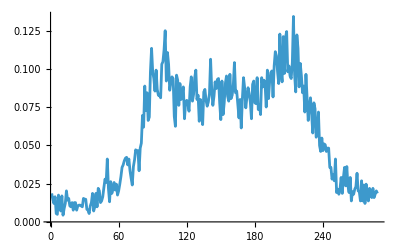

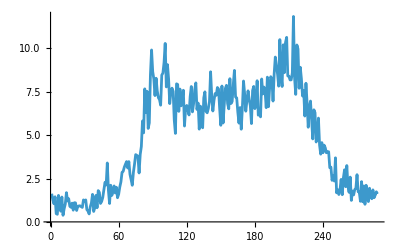

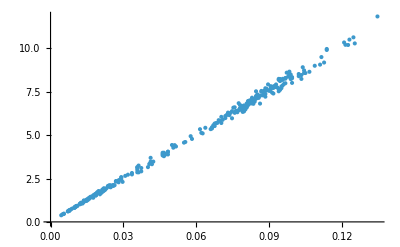

```mathematica
testRoad = GetSpeedAndDensityOfSingleRoad[55255453];
ListLinePlot[testRoad[[;;, 1]]]
ListLinePlot[testRoad[[;;, 2]]]
ListPlot[testRoad]
```

```mathematica
validNodes = VertexList[g];
$DefaultParallelKernels= {8};
CloseKernels[]
LaunchKernels[];
heatmapPoints = ParallelMap[GetSpeedAndDensityOfSingleRoad, validNodes, Method->"ItemsPerEvaluation" -> 10];
```

```mathematica
Export["heatmapPoints.mx", heatmapPoints];
```

```mathematica
heatmapPoints = Import["C:\\Users\\Matteo\\Documents\\heatmapPoints.mx"];
```

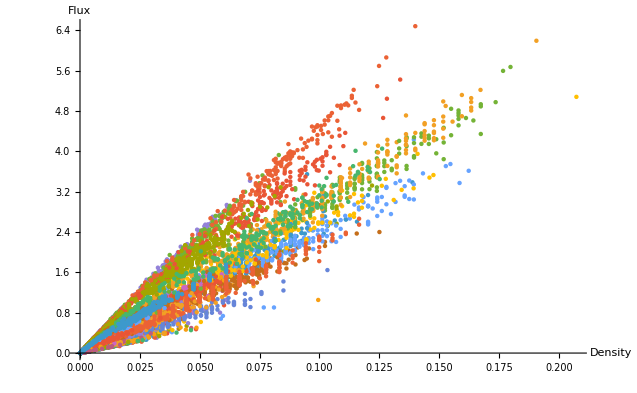

```mathematica
ListPlot[heatmapPoints[[200;;500]], AxesLabel->{"Density", "Flux"}, PlotStyle->PointSize[.005], PlotRange->Full]
```